```mathematica
z[t_]:= (E^(I*t)-(.3)E^(I*3*t)+(.2)E^(I*5*t))
```

```mathematica
z[t]
```

ⅇ^(ⅈ t)-0.3 ⅇ^(3 ⅈ t)+0.2 ⅇ^(5 ⅈ t)

```mathematica
z[0]
```

0.9

```mathematica
z[Pi/4]
```

0.777817+0.353553 ⅈ

```mathematica
"convert to exponential"0.7778174593052023+0.3535533905932737 ⅈWith[{n=Abs[0.7778174593052023+0.3535533905932737 ⅈ],a=Arg[0.7778174593052023+0.3535533905932737 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.8544 ⅇ^(ⅈ 0.426627)

```mathematica
z[Pi/2]
```

0.+1.5 ⅈ

```mathematica
"convert to exponential"0.+1.5 ⅈWith[{n=Abs[0.+1.5 ⅈ],a=Arg[0.+1.5 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

1.5 ⅇ^(ⅈ 1.5708)

```mathematica
z[3*Pi/4]
```

-0.777817+0.353553 ⅈ

```mathematica
"convert to exponential"-0.7778174593052022+0.35355339059327384 ⅈWith[{n=Abs[-0.7778174593052022+0.35355339059327384 ⅈ],a=Arg[-0.7778174593052022+0.35355339059327384 ⅈ]},Defer[n ⅇ^(ⅈ a)]]
```

0.8544 ⅇ^(ⅈ 2.71497)

```mathematica
z[Pi]
```

-0.9

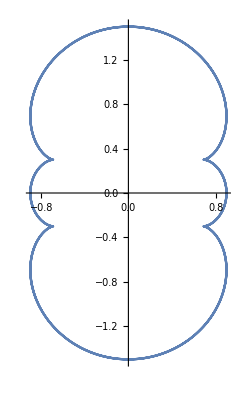

```mathematica
ParametricPlot[{Re[z[x]],Im[z[x]]},{x,0,6Pi}]
```